```mathematica
data1=Import["/Users/stshammi/temp/sky-avg-vs-monte-carlo/-1pn.csv","CSV"] ;
data2=Import["/Users/stshammi/temp/sky-avg-vs-monte-carlo/-1.5pn.csv","CSV"] ;data3=Import["/Users/stshammi/temp/sky-avg-vs-monte-carlo/-2pn.csv","CSV"] ;data4=Import["/Users/stshammi/temp/sky-avg-vs-monte-carlo/-2.5pn.csv","CSV"] ;data5=Import["/Users/stshammi/temp/sky-avg-vs-monte-carlo/-3pn.csv","CSV"] ;data6=Import["/Users/stshammi/temp/sky-avg-vs-monte-carlo/-3.5pn.csv","CSV"] ;
```

```mathematica
data7=Import["/Users/stshammi/temp/sky-avg-vs-monte-carlo/-4pn.csv","CSV"] ;
(*Above data are the values of beta at different PN orders from Monte-Carlo*)
dataSkyAvg=Import["/Users/stshammi/temp/sky-avg-vs-monte-carlo/sky-average.csv","CSV"] ;
```

```mathematica
dataSkyAvg (*beta,PN*)
```

{{6.4014718217604503693015067575772538×10^-9,-4.},{3.2112245517686812414925743634434945×10^-8,-3.5},{1.6538085441647248600269550041504183×10^-7,-3.},{8.8389557001037623059716451933899378×10^-7,-2.5},{4.9757539112269045846279757798613803×10^-6,-2.},{0.000029816351222357874109195258133659984,-1.5},{0.00017793511517792653013288086299615279,-1.}}

```mathematica
DynamicSetting[ColorSetter[]]
```

0.7

```mathematica
LineLegend[{Blue,Green},{"Sky-averaged","Mean value of Beta from Monte-Carlo"}]
```

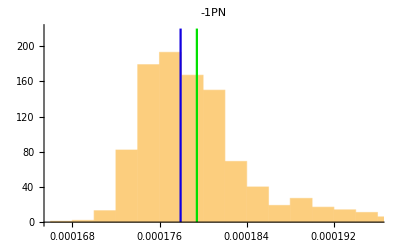

```mathematica
Show[Histogram[data1[[All,1]]],ListLinePlot[{{Mean[data1[[All,1]]],0},{Mean[data1[[All,1]]],220}},PlotStyle -> 0.],ListLinePlot[{{dataSkyAvg[[7,1]],0},{dataSkyAvg[[7,1]],220}},PlotStyle -> 0.07043564507515068],PlotLabel->"-1PN"]
```

```mathematica
(Mean[data1[[All,1]]]-dataSkyAvg[[7,1]])/Mean[data1[[All,1]]]*100
```

0.832255

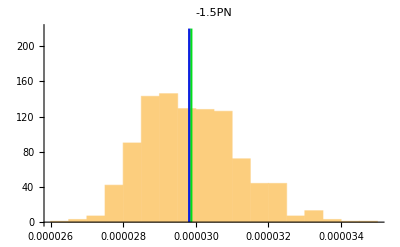

```mathematica
Show[Histogram[data2[[All,1]]],ListLinePlot[{{Mean[data2[[All,1]]],0},{Mean[data2[[All,1]]],220}},PlotStyle -> 0.],ListLinePlot[{{dataSkyAvg[[6,1]],0},{dataSkyAvg[[6,1]],220}},PlotStyle -> 0.05168230716411078],PlotLabel->"-1.5PN"]
```

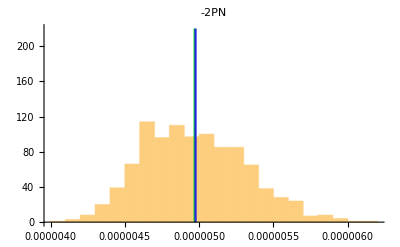

```mathematica
Show[Histogram[data3[[All,1]]],ListLinePlot[{{Mean[data3[[All,1]]],0},{Mean[data3[[All,1]]],220}},PlotStyle -> 0.],ListLinePlot[{{dataSkyAvg[[5,1]],0},{dataSkyAvg[[5,1]],220}},PlotStyle -> 0.15629816128786145],PlotLabel->"-2PN"]
```

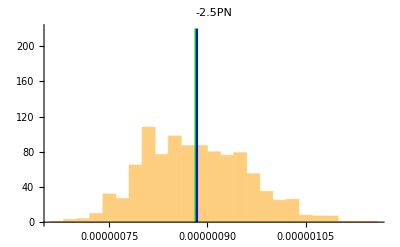

```mathematica
Show[Histogram[data4[[All,1]]],ListLinePlot[{{Mean[data4[[All,1]]],0},{Mean[data4[[All,1]]],220}},PlotStyle -> 0.],ListLinePlot[{{dataSkyAvg[[4,1]],0},{dataSkyAvg[[4,1]],220}},PlotStyle -> 0.0609597924773022],PlotLabel->"-2.5PN"]
```

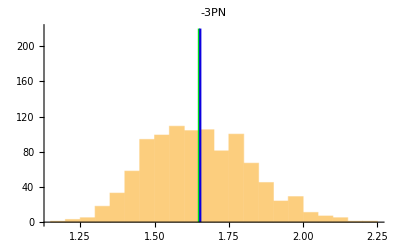

```mathematica
Show[Histogram[data5[[All,1]]],ListLinePlot[{{Mean[data5[[All,1]]],0},{Mean[data5[[All,1]]],220}},PlotStyle -> 0.],ListLinePlot[{{dataSkyAvg[[3,1]],0},{dataSkyAvg[[3,1]],220}},PlotStyle -> 0.047058823529411764],PlotLabel->"-3PN"]
```

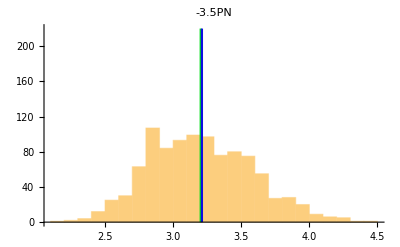

```mathematica
Show[Histogram[data6[[All,1]]],ListLinePlot[{{Mean[data6[[All,1]]],0},{Mean[data6[[All,1]]],220}},PlotStyle -> 0.],ListLinePlot[{{dataSkyAvg[[2,1]],0},{dataSkyAvg[[2,1]],220}},PlotStyle -> 0.049683375295643546],PlotLabel->"-3.5PN"]
```

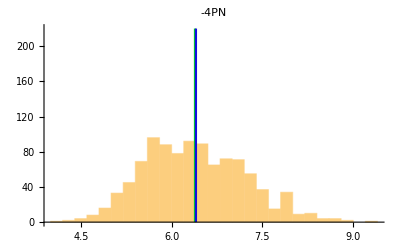

```mathematica
Show[Histogram[data7[[All,1]]],ListLinePlot[{{Mean[data7[[All,1]]],0},{Mean[data7[[All,1]]],220}},PlotStyle -> 0.],ListLinePlot[{{dataSkyAvg[[1,1]],0},{dataSkyAvg[[1,1]],220}},PlotStyle -> 0.0737773708705272],PlotLabel->"-4PN"]
```

```mathematica
Grid[{{PN,SkyAveraged,MonteCarlo,Difference:((MonteCarlo-SkyAveraged)/MonteCarlo*100)},{-1,dataSkyAvg[[7,1]],Mean[data1[[All,1]]],(Mean[data1[[All,1]]]-dataSkyAvg[[7,1]])/Mean[data1[[All,1]]]*100},{-1.5,dataSkyAvg[[6,1]],Mean[data2[[All,1]]],(Mean[data2[[All,1]]]-dataSkyAvg[[6,1]])/Mean[data2[[All,1]]]*100},{-2,dataSkyAvg[[5,1]],Mean[data3[[All,1]]],(Mean[data3[[All,1]]]-dataSkyAvg[[5,1]])/Mean[data3[[All,1]]]*100},{-2.5,dataSkyAvg[[4,1]],Mean[data4[[All,1]]],(Mean[data4[[All,1]]]-dataSkyAvg[[4,1]])/Mean[data4[[All,1]]]*100},{-3,dataSkyAvg[[3,1]],Mean[data5[[All,1]]],(Mean[data5[[All,1]]]-dataSkyAvg[[3,1]])/Mean[data5[[All,1]]]*100},{-3.5,dataSkyAvg[[2,1]],Mean[data6[[All,1]]],(Mean[data6[[All,1]]]-dataSkyAvg[[2,1]])/Mean[data6[[All,1]]]*100},{-4,dataSkyAvg[[1,1]],Mean[data7[[All,1]]],(Mean[data7[[All,1]]]-dataSkyAvg[[1,1]])/Mean[data7[[All,1]]]*100}},Frame->All]
```

PN | SkyAveraged | MonteCarlo | Difference:(100 (MonteCarlo-SkyAveraged))/MonteCarlo
-1 | 0.00017793511517792653013288086299615279 | 0.000179428 | 0.832255
-1.5 | 0.000029816351222357874109195258133659984 | 0.0000298754 | 0.19778
-2 | 4.9757539112269045846279757798613803×10^-6 | 4.96985×10^-6 | -0.118829
-2.5 | 8.8389557001037623059716451933899378×10^-7 | 8.81799×10^-7 | -0.237782
-3 | 1.6538085441647248600269550041504183×10^-7 | 1.64926×10^-7 | -0.27591
-3.5 | 3.2112245517686812414925743634434945×10^-8 | 3.20249×10^-8 | -0.272638
-4 | 6.4014718217604503693015067575772538×10^-9 | 6.38597×10^-9 | -0.242785